```mathematica
(*Calculamos la solución positiva de la ecuación x^2-3=0 con 14 cifras decimales exactas. Vamos a ver cuántas iteraciones serán necesarias en el intervalo inicial [1,2].

Veamos la resolución gráfica de la ecuación en el intervalo en cuestión:*)
f[x_]:=x^2-3
```

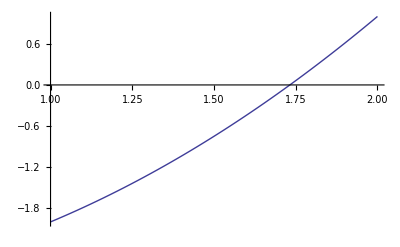

```mathematica
Plot[f[x],{x,1,2}]
```

```mathematica
(*La derivada de la función f es:*)
f'[x]
```

2 x

```mathematica
(*Habría ahora que ver cuándo se anula la derivada:*)
Solve[f'[x]==0]
```

{{x→0}}

```mathematica
(*Luego la única solución resulta ser x=0 y los intervalos de monotonía son (-∞,0) y (0,∞). Por tanto, solo hemos de comprobar la existencia de cambio de signo:*)
f[1]
f[2]
```

-2

1

```mathematica
(*Luego la única solución positiva está en el intervalo [1,2].

Para obtener una solución con 14 cifras decimales exactas estaríamos hablando de Subscript[E, A]≤ 10^(-14). Teniendo en cuenta la expresión del error absoluto para dicho error, tenemos que considerar (2-1)/2^n<10^(-14)*)
Log[2,10.^14]
```

46.507

```mathematica
(*Son 47 las iteraciones necesarias para obtener una aproximación de la solución.
Miramos la primera iteración y vamos haciendo el resto de iteraciones:*)
x0=1.`30
x1=2
x2=(x0+x1)/2
ea=Abs[x2-x1]
f[x0]
f[x1]
f[x2]
```

1.

2

1.5

0.5

-2.

1

-0.75

```mathematica
x3=(x1+x2)/2
ea=Abs[x3-x2]
f[x1]
f[x2]
f[x3]
```

1.75

0.25

1

-0.75

0.0625

```mathematica
x4=(x3+x2)/2
ea=Abs[x4-x3]
f[x2]
f[x3]
f[x4]
```

1.625

0.125

-0.75

0.0625

-0.359375

```mathematica
x5=(x4+x3)/2
ea=Abs[x5-x4]
f[x3]
f[x4]
f[x5]
```

1.6875

0.0625

0.0625

-0.359375

-0.15234375

```mathematica
x6=(x3+x5)/2
ea=Abs[x6-x5]
f[x3]
f[x5]
f[x6]
```

1.71875

0.03125

0.0625

-0.15234375

-0.0458984375

```mathematica
x7=(x3+x6)/2
ea=Abs[x7-x6]
f[x3]
f[x6]
f[x7]
```

1.734375

0.015625

0.0625

-0.0458984375

0.008056640625

```mathematica
x8=(x6+x7)/2
ea=Abs[x8-x7]
f[x6]
f[x7]
f[x8]
```

1.7265625

0.0078125

-0.0458984375

0.008056640625

-0.01898193359375

```mathematica
x9=(x7+x8)/2
ea=Abs[x9-x8]
f[x7]
f[x8]
f[x9]
```

1.73046875

0.00390625

0.008056640625

-0.01898193359375

-0.0054779052734375

```mathematica
x10=(x7+x9)/2
ea=Abs[x10-x9]
f[x7]
f[x9]
f[x10]
```

1.732421875

0.001953125

0.008056640625

-0.0054779052734375

0.001285552978515625

```mathematica
x11=(x9+x10)/2
ea=Abs[x11-x10]
f[x9]
f[x10]
f[x11]
```

1.7314453125

0.0009765625

-0.0054779052734375

0.001285552978515625

-0.00209712982177734375

```mathematica
(*Observa que el error absoluto cometido es de 3 cifras decimales exactas pese a haber realizado 11 iteraciones... *)
```